# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Solutions 09

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 1.

The hyperbolic absolute risk aversion (HARA) class of utility functions has the form

U[w]=(1-γ)/γ((a w)/(1-γ)+b)^γ ,   b>0

Show that the parameters of the HARA utility function can be chosen to obtain the following special cases:

Risk neutral: U[w]=w

Exponential: U[w]=-ⅇ^(-a w)    [Hint: Consider the limit γ→-∞]

Power: U[w]=a w^γ

Log: U[w]=ln[w]    [Hint: Consider U[w]=(1-γ)^(1-γ)((x^γ-1)/γ) and the limit γ→0]

#### Solution

```mathematica
hara=(1-γ)/γ((a w)/(1-γ)+b)^γ;
```

#### Linear

```mathematica
Limit[hara/.a->1,γ->1]
```

w

#### Exponential

```mathematica
Limit[hara/.b->1,γ->-∞]
```

-ⅇ^(-a w)

#### Power

```mathematica
Limit[hara/.a->1,b->0]
```

(w (w/(1-γ))^(-1+γ))/γ

… which can be simplified to

(1-γ)^(1-γ)/γ w^γ=c w^γ

#### Log

```mathematica
Limit[(1-γ)^(1-γ)/γ(w^γ-1),γ->0]
```

Log[w]

## Question 2.

You are given a random variate X which has a Student t distribution with PDF with 0<ν degrees of freedom. Let 𝔼[X^n] represent the n^th moment of X. Show mathematically which moments of X exist and which are indeterminate.

### Solution

The PDF of a Student t distributed random variable X with ν degrees of freedom is

f[x|ν]=(ν/(x^2+ν))^((1+ν)/2)/√νB[ν/2,1/2]

where B[a, b] is the Euler beta function.

For |x| sufficiently large and an appropriately chosen constant c

f[x|ν]=(c(1/(x^2+ν)))^((1+ν)/2)OverTilde[∝]x^(-(1+⋁))

The n^th moment is

𝔼[X^n]=∫_(-∞)^∞ x^n f[x|ν]ⅆx OverTilde[∝]∫_(-∞)^∞ x^(n-(1+⋁))ⅆx

For even moments, this converges for if n<ν. For odd moments, by symmetry, are zero if ν>1, but are indeterminate for 0<ν≤1.

## Question 3.

Consider the betting game below that we used to illustrate Kelly betting where we sought to maximize the growth rate.

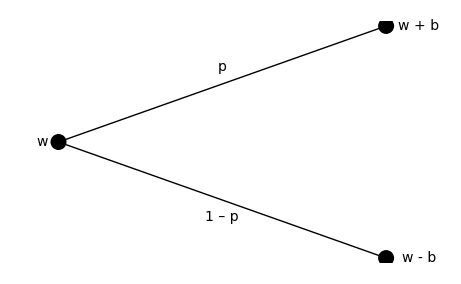

This led to solving for the bet b_Kelly^* which maximized the expected log wealth; i.e.,

b_Kelly^*=argmax_b[p log[w+b ]+(1+p) log[w-b]]

Now consider this game in the more general setting of utility theory where our goal will be to maximize the expected utility 𝔼[U[X]]; i.e.,

b^*=argmax_b[p U[w+b ]+(1+p)U[w-b]]

Let U[x]=√x.

Solve for the optimal bet for a player with square root utility for the game above.

Assume that the probability of winning p=0.6. Compare the Kelly bet with the square root utility bet.

For this game is the Kelly bet more aggressive, less aggressive, or sometimes more and sometimes less aggressive than the square root bet? Show how you came up with your answer.

### Solution

The solution for b_sqrt^* can be calculated by

```mathematica
Solve[D[(p √(w+b)+(1-p)√(w-b)), b]==0,b]
```

{{b→((-1+2 p) w)/(1-2 p+2 p^2)}}

Thus,

b_sqrt^*=(2p-1)/(2 p^2-2p+1)

The optimal bet for p=0.6 is to bet 38.5% of wealth at each round. The equivalent Kelly bet is 20%.

```mathematica
((-1+2 p) w)/(1-2 p+2 p^2)/.p->0.6
```

0.384615 w

Note that

b_sqrt^*/b_Kelly^*=1/(2 p^2-2p+1)

If we examine this ratio for 0.5<p<1 we see that the square root utility is more aggressive.

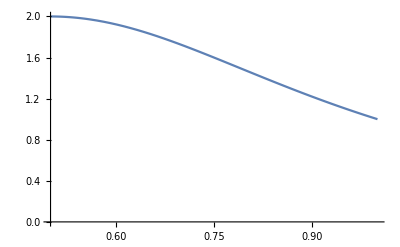

```mathematica
Plot[(2 p^2-2p+1)^-1,{p,0.5,1},AxesOrigin->{0.5,0}]
```